```mathematica
gaps1=Catenate@Get@FileNameJoin@{NotebookDirectory[],"gaps1.wl"};
gaps1[[All,1]]=1/gaps1[[All,1]];
```

```mathematica
gaps2=Catenate@Get@FileNameJoin@{NotebookDirectory[],"gaps2.wl"};
gaps2[[All,1]]=1/gaps2[[All,1]];
```

```mathematica
ListPointPlot3D@gaps1
```

-Graphics3D-

```mathematica
Fit[data, {1,x,x^2}, x]
```

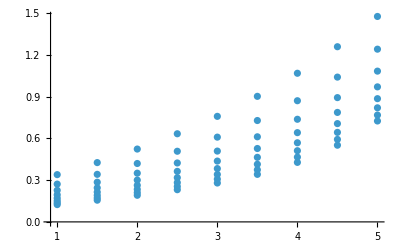

```mathematica
Show[ListPlot/@Table[Select[gaps1,#[[1]]==1/n&][[All,2;;]],{n,4,12}]]
```

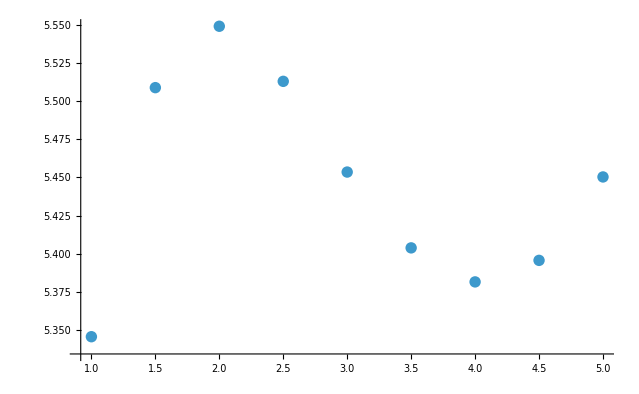

```mathematica
Show[ListPlot/@Table[Select[gaps2,#[[1]]==1/n&][[All,2;;]],{n,4,12}]]
```

```mathematica
gaps2
```

{{1/4,1.,5.34566},{1/4,1.5,5.50874},{1/4,2.,5.54894},{1/4,2.5,5.51287},{1/4,3.,5.45347},{1/4,3.5,5.40383},{1/4,4.,5.38155},{1/4,4.5,5.39565},{1/4,5,5.45027},{1/5,1.,4.333},{1/5,1.5,4.54653},{1/5,2.,4.64787},{1/5,2.5,4.63792},{1/5,3.,4.56821},{1/5,3.5,4.48848},{1/5,4.,4.42894},{1/5,4.5,4.40609},{1/5,5,4.42847},{1/6,1.,3.59575},{1/6,1.5,3.8244},{1/6,2.,3.96384},{1/6,2.5,3.9851},{1/6,3.,3.92087},{1/6,3.5,3.82864},{1/6,4.,3.74927},{1/6,4.5,3.70618},{1/6,5,3.71215},{1/7,1.,3.05648},{1/7,1.5,3.28275},{1/7,2.,3.43944},{1/7,2.5,3.48506},{1/7,3.,3.4306},{1/7,3.5,3.33367},{1/7,4.,3.2432},{1/7,4.5,3.18864},{1/7,5,3.18664},{1/8,1.,2.6523},{1/8,1.5,2.86878},{1/8,2.,3.0302},{1/8,2.5,3.09228},{1/8,3.,3.04781},{1/8,3.5,2.94986},{1/8,4.,2.85309},{1/8,4.5,2.79205},{1/8,5,2.78693},{1/9,1.,2.34082},{1/9,1.5,2.54492},{1/9,2.,2.70445},{1/9,2.5,2.77677},{1/9,3.,2.74125},{1/9,3.5,2.64407},{1/9,4.,2.5438},{1/9,4.5,2.47931},{1/9,5,2.47404},{1/10,1.,2.09442},{1/10,1.5,2.28574},{1/10,2.,2.44018},{1/10,2.5,2.51839},{1/10,3.,2.49046},{1/10,3.5,2.39495},{1/10,4.,2.2929},{1/10,4.5,2.2269},{1/10,5,2.22334},{1/11,1.,1.895},{1/11,1.5,2.07408},{1/11,2.,2.22203},{1/11,2.5,2.30323},{1/11,3.,2.28162},{1/11,3.5,2.18822},{1/11,4.,2.08549},{1/11,4.5,2.01923},{1/11,5,2.01861}}